```mathematica
2+2
```

4

```mathematica
f[x_]=x∫_x^∞ BesselK[5/3,x]ⅆx;
g[x_]= x BesselK[2/3,x];
```

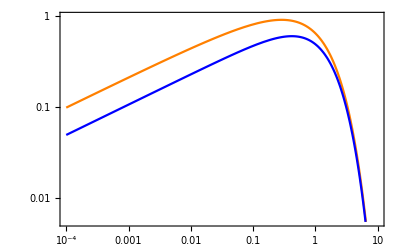

```mathematica
LogLogPlot[{f[x],g[x]},{x,10^-4,10},Frame->True,PlotStyle->{Orange,Blue}]
```

### Assymptotic expansion of modified Bessel functions for small/large z

```mathematica
KS[ν_,z_]= Gamma[ν]/2(2/z)^ν;KL[ν_,z_]= √(π/(2z))ⅇ^-z(1+(4 ν^2-1)/(8z)+((4 ν^2-1)(4 ν^2-9))/(2! 8 z^2));
```

### First the G (x) functions

```mathematica
gS[z_]=FullSimplify[z KS[2/3,z]]
gL[z_]=FullSimplify[z KL[2/3,z]]
```

Gamma[2/3]/(2^(1/3) (1/z)^(1/3))

(ⅇ^-z √(π/2) (1/z)^(3/2) (-455+18 z (7+72 z)))/1296

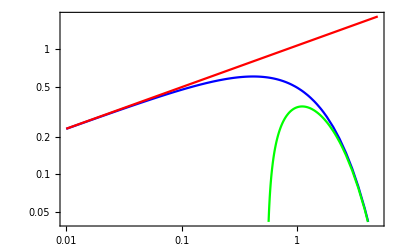

```mathematica
LogLogPlot[{g[x],gS[x],gL[x]},{x,10^-2,5},Frame->True,PlotStyle->{Blue,Red, Green}]
```

### Now the F(x) functions

```mathematica
fS[z_]=FullSimplify[z ∫_z^∞ KS[5/3,x]ⅆx, Assumptions->{z ∈ Reals,z>0}]
fL[z_]=FullSimplify[z ∫_z^∞ KL[5/3,x]ⅆx, Assumptions->{z ∈ Reals,z>0}]
```

2^(2/3) z^(1/3) Gamma[2/3]

(√(π/2) z ((91 ⅇ^-z (19+16 z))/z^(3/2)+488 √π Erfc[√z]))/1944

Now introduce an expansion of the Erfc function

```mathematica
fL2[z_]=(√(π/2) z ((91 ⅇ^-z (19+16 z))/z^(3/2)+488 √π(1/6 ⅇ^-z+1/2 ⅇ^(-(4/3)z)) ))/1944
```

(√(π/2) z (488 (1/2 ⅇ^(-4 z/3)+ⅇ^-z/6) √π+(91 ⅇ^-z (19+16 z))/z^(3/2)))/1944

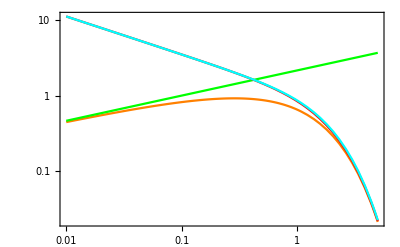

```mathematica
LogLogPlot[{f[x],fS[x],fL[x], fL2[x]},{x,10^-2,5},Frame->True,PlotStyle->{Orange,Green,Red, Cyan}]
```

### This are the small/large x expressions that are going to be used in the code

### For F (x)

```mathematica
ExpandAll[fS[x]]//N
FullSimplify[ExpandAll[fL2[x]]]//N
```

2.14953 x^(1/3)

0.278823 2.71828^(-1.33333 x) x+(0.000214903 2.71828^(-1. x) (5187.+4368. x+432.479 x^(3/2)))/(√x)

#### For G (x)

```mathematica
ExpandAll[gS[x]]//N
FullSimplify[ExpandAll[gL[x]]//N]
```

1.07476/(1/x)^(1/3)

1.25331 ⅇ^(-1. x) (1/x)^(3/2) (-0.35108+x (0.0972222+1. x))

### Now Lets do tables for a range in x between 0.01 and 5

#### Log spaced numbers

```mathematica
{a,b,c}={0.01,100,5};
t=(c/a)^(1/b)//N ;
Xlist = a*t^Range[b];
Flist := {}
Glist := {}
```

```mathematica
For[i=1,i<101,i++,{AppendTo[Flist,f[ Xlist[[i]]]],AppendTo[Glist,g[ Xlist[[i]]]]}]
```

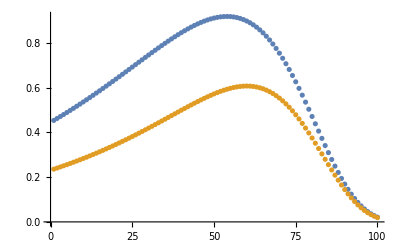

```mathematica
ListPlot[{Flist,Glist}]
```

#### Write to textfiles

```mathematica
Export["Xlist.txt",Xlist]
Export["Flist.txt",Flist]
Export["Glist.txt",Glist]
```

Xlist.txt

Flist.txt

Glist.txt

```mathematica
datos:={Xlist,Flist,Glist}
```

```mathematica
MatrixForm[Transpose[datos]]
```

(0.0106412 | 0.453504 | 0.235766
0.0113235 | 0.462165 | 0.240646
0.0120495 | 0.470953 | 0.245623
0.0128221 | 0.479869 | 0.250697
0.0136442 | 0.488911 | 0.25587
0.014519 | 0.498078 | 0.261144
0.01545 | 0.507369 | 0.266519
0.0164406 | 0.516782 | 0.271997
0.0174947 | 0.526315 | 0.277579
0.0186165 | 0.535965 | 0.283266
0.0198101 | 0.54573 | 0.289059
0.0210803 | 0.555607 | 0.294959
0.0224319 | 0.565592 | 0.300967
0.0238702 | 0.575682 | 0.307083
0.0254007 | 0.58587 | 0.313308
0.0270293 | 0.596154 | 0.319641
0.0287624 | 0.606527 | 0.326084
0.0306066 | 0.616983 | 0.332635
0.032569 | 0.627516 | 0.339295
0.0346572 | 0.638118 | 0.346063
0.0368794 | 0.648781 | 0.352938
0.039244 | 0.659497 | 0.359918
0.0417603 | 0.670255 | 0.367003
0.0444378 | 0.681046 | 0.374189
0.0472871 | 0.691858 | 0.381474
0.050319 | 0.702679 | 0.388856
0.0535454 | 0.713496 | 0.396331
0.0569786 | 0.724295 | 0.403895
0.0606319 | 0.735059 | 0.411542
0.0645195 | 0.745773 | 0.419267
0.0686563 | 0.756419 | 0.427064
0.0730584 | 0.766977 | 0.434926
0.0777428 | 0.777428 | 0.442845
0.0827275 | 0.787749 | 0.450811
0.0880318 | 0.797917 | 0.458814
0.0936762 | 0.807906 | 0.466843
0.0996825 | 0.817691 | 0.474885
0.106074 | 0.827243 | 0.482926
0.112875 | 0.836531 | 0.49095
0.120112 | 0.845525 | 0.49894
0.127814 | 0.854189 | 0.506878
0.136009 | 0.86249 | 0.514743
0.14473 | 0.870388 | 0.522512
0.154009 | 0.877844 | 0.530161
0.163884 | 0.884818 | 0.537662
0.174392 | 0.891264 | 0.544988
0.185573 | 0.897138 | 0.552106
0.197472 | 0.902391 | 0.558983
0.210134 | 0.906976 | 0.565584
0.223607 | 0.91084 | 0.571868
0.237944 | 0.91393 | 0.577796
0.2532 | 0.916193 | 0.583323
0.269435 | 0.917572 | 0.588403
0.286711 | 0.918011 | 0.592986
0.305094 | 0.917452 | 0.597022
0.324656 | 0.915838 | 0.600457
0.345472 | 0.913109 | 0.603235
0.367623 | 0.90921 | 0.605299
0.391194 | 0.904083 | 0.60659
0.416277 | 0.897674 | 0.607047
0.442967 | 0.889929 | 0.606611
0.471369 | 0.880801 | 0.605221
0.501593 | 0.870244 | 0.602817
0.533754 | 0.858217 | 0.599341
0.567977 | 0.844687 | 0.594738
0.604394 | 0.829627 | 0.588957
0.643146 | 0.813019 | 0.581949
0.684384 | 0.794855 | 0.573674
0.728265 | 0.775136 | 0.564097
0.774959 | 0.753878 | 0.553194
0.824648 | 0.731109 | 0.54095
0.877523 | 0.706873 | 0.527362
0.933788 | 0.68123 | 0.51244
0.99366 | 0.654255 | 0.496209
1.05737 | 0.626044 | 0.478709
1.12517 | 0.59671 | 0.459999
1.19731 | 0.566384 | 0.440155
1.27408 | 0.535219 | 0.419272
1.35577 | 0.503381 | 0.397463
1.4427 | 0.471057 | 0.374863
1.5352 | 0.438449 | 0.35162
1.63364 | 0.405769 | 0.327903
1.73838 | 0.373242 | 0.303893
1.84984 | 0.3411 | 0.279784
1.96845 | 0.309575 | 0.255778
2.09466 | 0.278898 | 0.232083
2.22897 | 0.249293 | 0.208904
2.37188 | 0.220972 | 0.186445
2.52396 | 0.194127 | 0.164897
2.6858 | 0.168928 | 0.144436
2.858 | 0.145518 | 0.125218
3.04125 | 0.124005 | 0.107373
3.23625 | 0.104463 | 0.0910028
3.44375 | 0.0869282 | 0.0761756
3.66456 | 0.0713976 | 0.0629258
3.89952 | 0.057831 | 0.0512533
4.14955 | 0.0461527 | 0.0411244
4.41561 | 0.0362554 | 0.0324745
4.69873 | 0.0280052 | 0.0252117
5. | 0.0212481 | 0.0192221)

```mathematica
Export["datos.txt",Transpose[datos]]
```

datos.txt

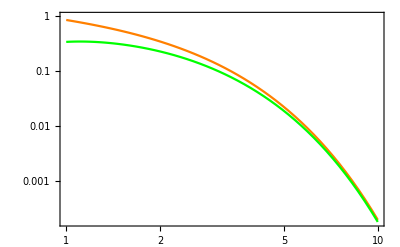

```mathematica
LogLogPlot[{fL2[x],gL[x]},{x,10^0,10},Frame->True,PlotStyle->{Orange,Green}]
```

```mathematica
fL2[30]//N
gL[30]//N
```

7.61109×10^-13

6.44202×10^-13